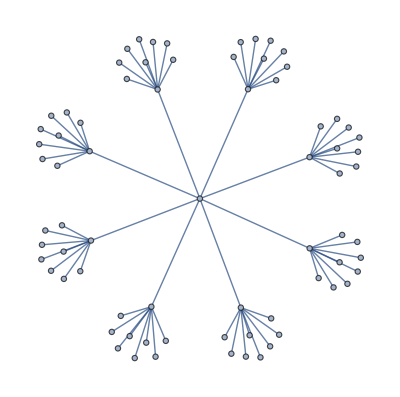

-Graphics-

```mathematica
g=CompleteKaryTree[3,8]
```

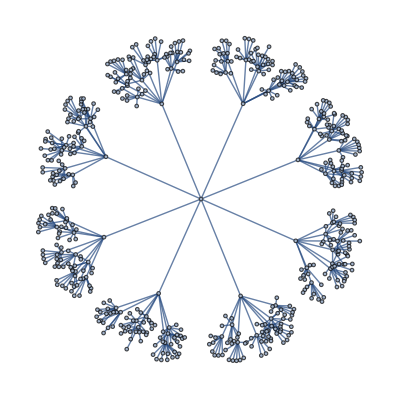

-Graphics-

```mathematica
g=CompleteKaryTree[4,8]
```

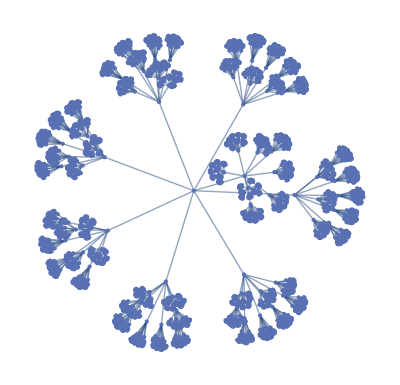

```mathematica
g=CompleteKaryTree[5,8]
```

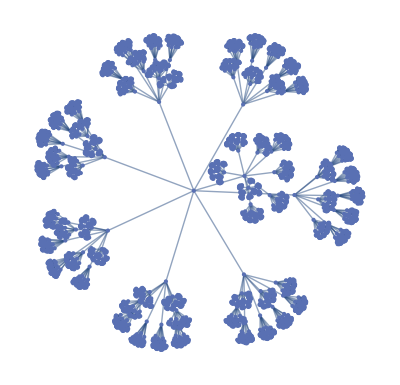

-Graphics-

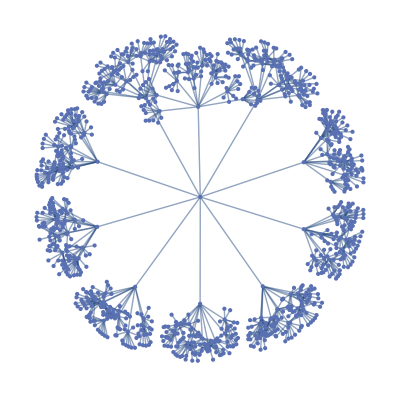

```mathematica
g=CompleteKaryTree[4,10]
```

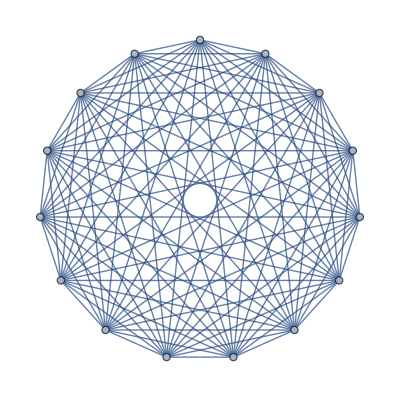

-Graphics-

```mathematica
g=CompleteGraph[15]
```

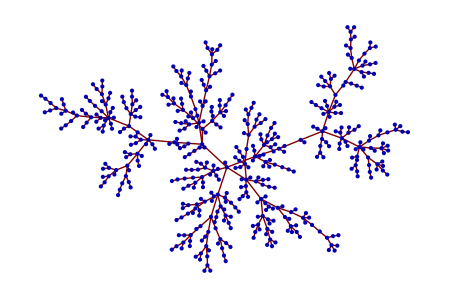

```mathematica
g=RandomInteger[#]->#+1&/@Range[0,500];
GraphPlot[g,Method->{"SpringElectricalEmbedding","RepulsiveForcePower"->-2}]
```

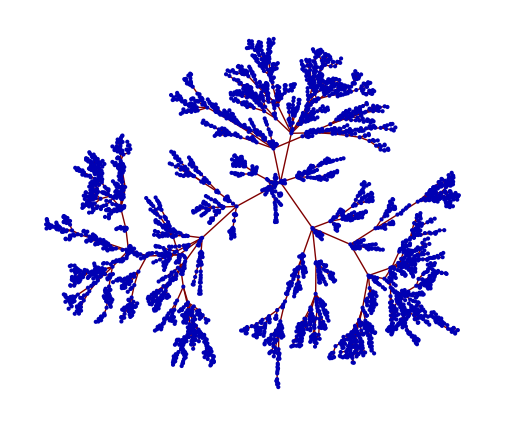

```mathematica
g=RandomInteger[#]->#+1&/@Range[0,4000];
GraphPlot[g,Method->{"SpringElectricalEmbedding","RepulsiveForcePower"->-1}]
```

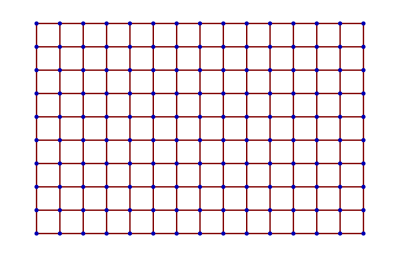

```mathematica
GraphPlot[GridGraph[{10,15}],Method->"SpringElectricalEmbedding"]
```

-Graphics-

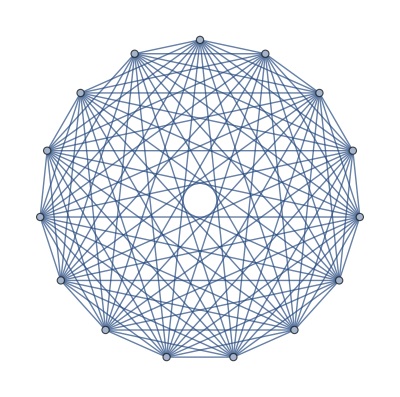

```mathematica
g=CompleteGraph[15]
EdgeDelete[g,1->2]
```

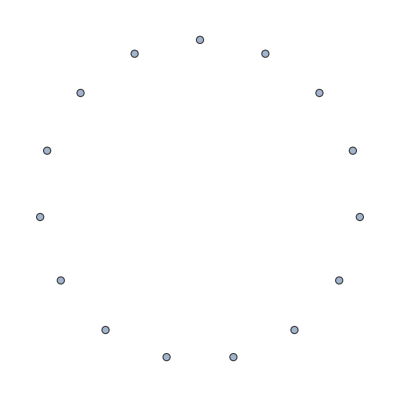

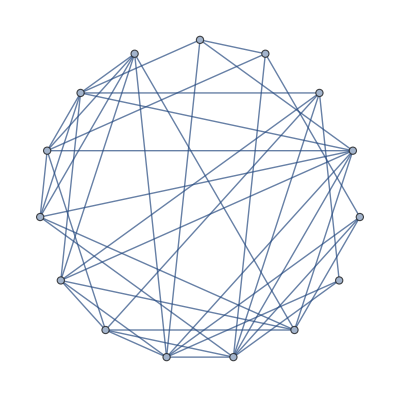

-Graphics-

```mathematica
v=15;

p=0;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list]

p=0.5;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list]

p=1;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list]
```

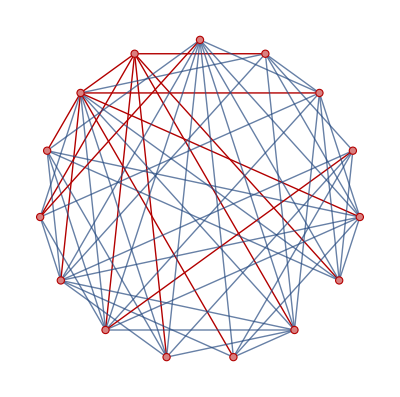

```mathematica
p=0.6;
v=15;
g=CompleteGraph[v];
list=Flatten[Table[If[Random[]>p,i->j,Nothing],{i,1,v},{j,i+1,v}]];
g=EdgeDelete[g,list];
mst=FindSpanningTree[g];
HighlightGraph[g,mst,GraphHighlightStyle->"Thick"]
```